```mathematica
(*1 a*)
mass = 1500(*kg*);
speed = 1000(*m/s*);
h0 = 3(*m*);
g = 9.81(*m/s^2*);
angle = 40 Degree;
vx = speed * Cos[angle];
vy0 = speed * Sin[angle];
MyPosition[x0_,v_,a_,t_]:=x0+v*t+0.5*a*t^2
```

```mathematica
stoptime = Solve[MyPosition[h0,vy0,-g,t]==0 && t>0,t];
t1 = t/.stoptime[[1]];
```

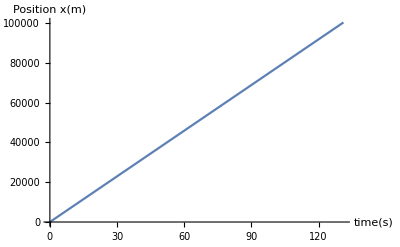

```mathematica
Plot[MyPosition[0,vx,0,t],{t,0,t1},AxesLabel->{"time(s)","Position x(m)"}]
```

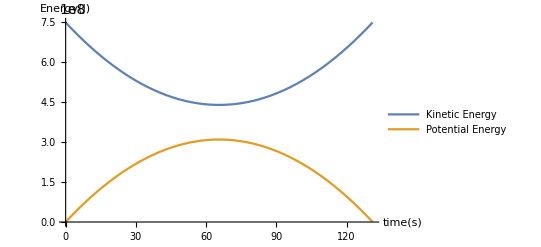

```mathematica
(*1 b*)
vy[t_]:= vy0 - g*t
KineticEnergy[t_]:=0.5*mass*(vy[t]^2+vx^2)
PotentialEnergy[t_]:=mass*g*MyPosition[h0,vy0,-g,t]
Plot[{KineticEnergy[t],PotentialEnergy[t]},{t,0,t1},PlotLegends->{"Kinetic Energy","Potential Energy"},AxesLabel->{"time(s)","Energy(J)"}]
```

```mathematica
(*1 c*)
Y[t_,varyangle_]:=MyPosition[h0,speed*Sin[varyangle],-g,t]
X[t_,varyangle_]:=MyPosition[0,speed*Cos[varyangle],0,t]
Distance[varyangle_]:=Module[ {Sol=Solve[Y[t,varyangle]==0&&t>0,t]},
Integrate[Sqrt[D[X[t,varyangle],t]^2+D[Y[t,varyangle],t]^2],{t,0,t/.Sol[[1]]}]]
Manipulate[Distance[varyangle],{varyangle,0,0.5*Pi}]
```

```mathematica
(*1 d*)
T[x_,varyangle_]:=x/(speed * Cos[varyangle])
YX[x_,varyangle_]:=Y[t,varyangle]/.t->T[x,varyangle]
MyPlot[varyangle_]:=Module[{Sol ,xmax},
Sol = Solve[YX[x,varyangle]==0&&x>0,x];
xmax=x/.Sol;
Plot[YX[x,varyangle],{x,0,xmax[[1]]}]]
Manipulate[MyPlot[varyangle],{varyangle,0,0.5*Pi}]
```

```mathematica
(*2a*)
(*
Here are some defination of variables with units
*)
pTotal = 1(*Gev/c*);
By=2*0.3(*Gv/mc*);
q=-1(*e*);
m=0.000511`3(*Gev/c^2*);
v=Sqrt[pTotal^2/(m^2+pTotal^2)] (*m/s*);
gamma = Sqrt[1/(1-v^2)];
```

```mathematica
(*
Sol1 is the solution of the differential equation sets.
*)
```

```mathematica
Sol1 = NDSolve[{q*vz[z]*By==-m*(vz[z]*vz'[z]*x'[z]+vz[z]^2*x''[z])*gamma,q*vz[z]*x'[z]*By==m*vz[z]*vz'[z]*gamma,x[0]==0,vz[0]*x'[0]==0.,vz[0]==v},{x,vz},{z,0,1}];
x1[z_]:=x[z]/.Sol1[[1]][[1]];
vz1final[z_]:=vz[z]/.Sol1[[1]][[2]];
vx1final=Sqrt[v^2-vz1final[1]^2];
px1final= gamma*vx1final*m ;
pz1final=gamma*vz1final[1]*m;
{x1[1],px1final,pz1final}
(*2a answer
  x1 = 0.333333, y1 = 0, z1 = 1
px1 = 0.6,     py1 = 0,pz1 = 0.8
*)
```

{0.333333,0.6,0.8}

```mathematica
(*2b*)
(*(0,-0.05Gev/c)*)
px2 = -0.05;
pz2 = Sqrt[pTotal^2-px2^2];
vx2 = px2/(gamma*m);
vz2 = Sqrt[v^2-vx2^2];
vx2/vz2 (*The initial condition of x'[0] should be this*);
```

```mathematica
Sol2 =NDSolve[{q*vz[z]*By==-m*(vz[z]*vz'[z]*x'[z]+vz[z]^2*x''[z])*gamma,q*vz[z]*x'[z]*By==m*vz[z]*vz'[z]*gamma,x[0]==0,x'[0]==vx2/vz2,vz[0]==vz2},{x,vz},{z,0,1}];
x2[z_]:=x[z]/.Sol2[[1]][[1]];
vz2final[z_]:=vz[z]/.Sol2[[1]][[2]];
pz2final = vz2final[1]*gamma*m;
px2final = Sqrt[pTotal^2-pz2final^2];
{x2[1],px2final,pz2final}
```

{0.272641,0.55,0.835165}

0.759934

0.65

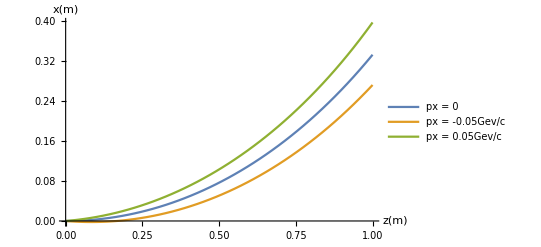

```mathematica
(*(0,0.05Gev/c)*)
Sol3 =NDSolve[{q*vz[z]*By==-m*(vz[z]*vz'[z]*x'[z]+vz[z]^2*x''[z])*gamma,q*vz[z]*x'[z]*By==m*vz[z]*vz'[z]*gamma,x[0]==0,x'[0]==-vx2/vz2,vz[0]==vz2},{x,vz},{z,0,1}];
x3[z_]:=x[z]/.Sol3[[1]][[1]];
vz3final[z_]:=vz[z]/.Sol3[[1]][[2]];
pz3final = vz3final[1]*gamma*m
px3final = Sqrt[pTotal^2-pz3final^2]
Plot[{x1[z],x2[z],x3[z]},{z,0,1},PlotLegends->{"px = 0", "px = -0.05Gev/c","px = 0.05Gev/c"},AxesLabel->{"z(m)","x(m)"}]
(*
Comments: as the velocity vectors are perpendicular to magnetic field vectors, therefore, the path of electrons would be a part of a circle. As the px increased, the circule is rotated, therefore, the parts are rotated.
*)
```

```mathematica
(*2 c*)
finalXPx[{xinit_,pxinit_}]:=
Module[{pz=Sqrt[pTotal^2-pxinit^2],Sol,vx0,vz0,xfunction,vzfunction,pxfinal,vxfinal},vx0=pxinit/(m*gamma);vz0=Sqrt[v^2-vx0^2];
Sol=NDSolve[{q*vz[z]*By==-m*(vz[z]*vz'[z]*x'[z]+vz[z]^2*x''[z])*gamma,q*vz[z]*x'[z]*By==m*vz[z]*vz'[z]*gamma,x[0]==xinit,x'[0]==vx0/vz0,vz[0]==vz0},{x,vz},{z,0,1}];
xfunction:=x/.Sol[[1]][[1]];
vzfunction:=vz/.Sol[[1]][[2]];
vxfinal = Sqrt[v^2-vzfunction[1]^2];
pxfinal=gamma*m*vxfinal;
{xfunction[1],pxfinal}]
```

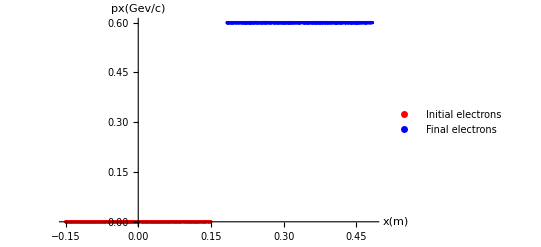

```mathematica
numberelectrons = 1000;
electronsInitial={};
For[i=1,i<=numberelectrons,i++,electronsInitial = Insert[electronsInitial,{RandomReal[{-0.15,0.15}],RandomReal[{-0.0007,0.0007}]},-1]]
electronsFinal = {};
For[i=1,i<=numberelectrons,i++,electronsFinal = Insert[electronsFinal,finalXPx[electronsInitial[[i]]],-1]]
ListPlot[{electronsInitial,electronsFinal},PlotStyle->{Red,Blue},PlotLegends->{"Initial electrons","Final electrons"},AxesLabel->{"x(m)","px(Gev/c)"}]
```

```mathematica
(*2d*)
rms[List_]:=Module[{squaremean=0,meansquare=0},
For[i=1,i<=numberelectrons,i++,
squaremean += List[[i]][[1]]^2;
meansquare+=List[[i]][[1]]];
squaremean /=numberelectrons;
meansquare /=numberelectrons;
meansquare=meansquare^2;
Sqrt[squaremean-meansquare]]
electronsInitial[[1]];
electronsInitial[[2]];
rms[electronsInitial]
rms[electronsFinal]
(*
The first output is the rms of Initial electrons. The second output is the rms of the Final electrons
*)
```

0.0857131

0.0856977

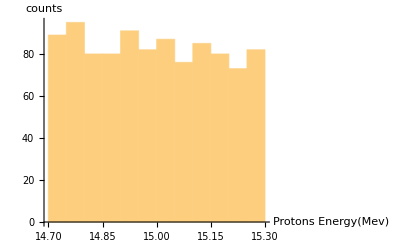

```mathematica
(*3a*)
spread=0.02;
meanEnergy=15;
mass=938.27208816 (*Mev*);
meanEnergyMin=meanEnergy*(1-spread);
meanEnergyMax=meanEnergy*(1+spread);
protonsEnergy=RandomReal[{meanEnergyMin,meanEnergyMax},1000];
Histogram[protonsEnergy,AxesLabel->{"Protons Energy(Mev)","counts"}]
```

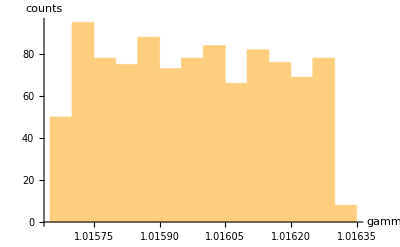

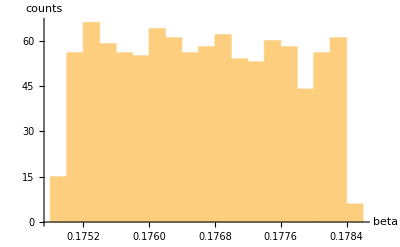

```mathematica
(*3b*)
gamma = protonsEnergy / mass+1;
velocity = Sqrt[(gamma^2-1)]/gamma*c;
beta = velocity / c;
Histogram[gamma,AxesLabel->{"gamma","counts"}]
Histogram[beta,AxesLabel->{"beta","counts"}]
```

```mathematica
(*3c*)
protonsEnergytotal = protonsEnergy + mass;
length = 2.664;
c = 299792458;
velocity = Sqrt[(gamma^2-1)]/gamma*c;
time = length / velocity;
points={};
For[i=1,i<=1000,i++,points=Insert[points,{time[[i]],protonsEnergytotal[[i]]},-1]]
```

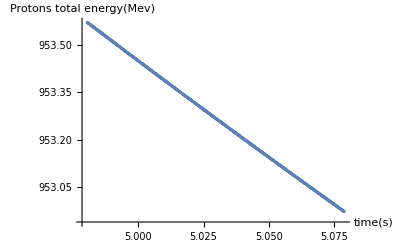

```mathematica
ListPlot[points,AxesLabel->{"time(s)","Protons total energy(Mev)"}]
```

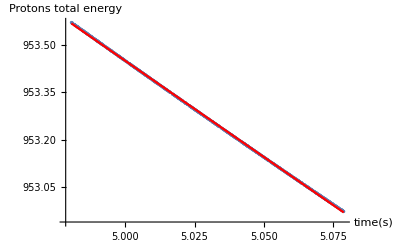

```mathematica
(*3d*)
model = a*t+b;
lm = FindFit[points,model,{a,b},t];
Show[ListPlot[points],Plot[model/.lm,{t,Min[time],Max[time]},PlotStyle->Red],AxesLabel->{"time(s)","Protons total energy"}]
```